```mathematica
Self-consistent shooting method to find weak coexistence densities+numerical results for β=1/2
```

```mathematica
Clear everthing
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Original equation, \partial_x\mu=F, encapsulated by operator, LO, in terms of implicit variables v and J
```

```mathematica
LO[β_,Pe_,v_,J_]:=Pe*D[ϕ[x]*(1-ϕ[x]),x]-D[(D[ϕ[x],x]+v*ϕ[x]+J)/(Pe*(1-ϕ[x])),{x,2}]-v*D[(D[ϕ[x],x]+v*ϕ[x]+J)/(Pe*(1-ϕ[x])),x]-(((1+β)^2)/(2*β*Pe))*D[Log[1-ϕ[x]],x]+(((1+β)^2)/(2*β))*(v*ϕ[x]+J)/(Pe*(1-ϕ[x]))-(1-β*β)*ϕ[x]/(2*β)
(*Print["Operator LO:  ",TraditionalForm[LO[β,Pe,v,J]]==0];*)
```

```mathematica
Operator, L, appearing in maintext, in terms of implicit variables ρG and ρL
```

```mathematica
L=FullSimplify[LO[β,Pe,v,J]/.{v->Pe*((1-β)/(1+β))*(1-ρG-ρL),J->Pe*((1-β)/(1+β))*ρG*ρL}];
(*Print["Operator L:  ",TraditionalForm[L/.{ρG->Subscript[ρ, G],ρL->Subscript[ρ, L]}]==0];*)
```

```mathematica
Take numerator for easier integration
```

```mathematica
LNumerator=Numerator[L];
(*Print["Numerator of operator L: ",TraditionalForm[LNumerator/.{ρG->Subscript[ρ, G],ρL->Subscript[ρ, L]}]==0]*)
```

```mathematica
Wrap this condition into a function of shooting parameters that defines an ODE to be integrated- explicitly, we integrate LODE[ϕ]=0 from one bulk (ρL) to another (ρG) with ρL > ρG
```

```mathematica
LODE[β_?NumericQ,Pe_?NumericQ,ρL_?NumericQ,ρG_?NumericQ]=LNumerator;
```

```mathematica
Objective function and solution-integrates from x=0 at ρ=ρL until solution leaves solution envelope (p[x]∈ [0,1]).
```

```mathematica
solutionAndObjFn[β_?NumericQ (*" control parameter "*),Pe_?NumericQ(*" control parameter "*),ρL_?NumericQ(*" liquid density implicit parameter"*),ρG_?NumericQ(*" gaseous density implicit parameter"*),dϕdx_?NumericQ (*" initial condition (1st derivative) parameter"*),d2ϕdx2_?NumericQ(*" initial condition (2nd derivative) parameter"*)]:=Module[{xboundFlag=False,xmidFlag=False,xleave =1000,xbound=1000,xmid=0},

(*"
	calculate result of integration, sol (i.e. the result of the "shooting" step)
	ODE to be solved:
		LHatODE[β,Pe,ρL,ρG]==0
	Three initial conditions in terms of small (and negative) ϵ = -10^(-10)
		1: ϕ[0]==pL+ϵ (i.e. start a small delta below self consistent liquid density parameter
		2: ϕ'[0]==dϕdx*ϵ (i.e. start with a small negative first derivative, assuming dϕdx > 0)
		3: ϕ''[0]==d2ϕdx2*ϵ (i.e. start with a small negative second derivative, assuming d2ϕdx2 > 0)
	On event commands:
		WhenEvent[((ϕ[x]≥1))||((ϕ[x]<0)),xleave=x;"StopIntegration"]     
			Stop integrating when ϕ[x] leaves [0,1] and record position this occurs with xleave.
		WhenEvent[((ϕ'[x]>SetPrecision[10^(-10),50])&&(x>1)&&(xboundFlag==False))&&(xmidFlag==True),xbound=x;xboundFlag=True]
			Record when gradient becomes positive (after a small initial delta and after ϕ[x] meets midway point) for the first time with xbound(we anticipate a monotonically decreasing function)
		WhenEvent[(Abs[ϕ[x]-pG]<Abs[ϕ[x]-pL])&&(xmidFlag==False),xmid=x;xmidFlag=True]
			Record when ϕ[x] gets closer to ρG than ρL for the first time with xmid (we anticipate a monotonically decreasing function)
   "*)

sol=NDSolve[{LODE[β,Pe,ρL,ρG]==0,ϕ[0]==ρL+ϵ,ϕ'[0]==dϕdx*ϵ,ϕ''[0]==d2ϕdx2*ϵ,WhenEvent[((ϕ[x]≥1))||((ϕ[x]<0)),xleave=x;"StopIntegration"],WhenEvent[((ϕ'[x]>SetPrecision[10^(-10),50])&&(x>1)&&(xboundFlag==False))&&(xmidFlag==True),xbound=x;xboundFlag=True],WhenEvent[(Abs[ϕ[x]-ρG]<Abs[ϕ[x]-ρL])&&(xmidFlag==False),xmid=x;xmidFlag=True]}/.{ϵ->SetPrecision[-10^(-10),50]},ϕ[x],{x,0,1000},WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25,MaxStepSize->0.005,MaxSteps->Infinity,Compiled->False][[1]][[1]][[2]];

(*"
		take numerical derivatives of solution
   "*)

Ds=D[sol,x];
D2s=D[sol,{x,2}];
D3s=D[sol,{x,3}];

(*"
		Find minimum of function used as distance from a bulk gaseous state: (ϕ[x]-ρG)^2 + (ϕ'[x])^2 + (ϕ''[x])^2 + (ϕ'''[x])^2
		To improve performance/reduce errors we search on plausible region [xmid, Min[xleave,xbound]] formed of captured variables in WhenEvent conditions in above integration
		We perform several searches starting at different points on this interval to maximise chance of finding the true minimimum
   "*)

values={Flatten[FindMinimum[{(sol-ρG)*(sol-ρG)+Ds*Ds+D2s*D2s+D3s*D3s,xmid≤x≤Min[xleave,xbound]},{x,xmid},AccuracyGoal->70,PrecisionGoal->70]],Flatten[FindMinimum[{(sol-ρG)*(sol-ρG)+Ds*Ds+D2s*D2s+D3s*D3s,xmid≤x≤Min[xleave,xbound]},{x,Min[xleave,xbound]},AccuracyGoal->70,PrecisionGoal->70]],Flatten[FindMinimum[{(sol-ρG)*(sol-ρG)+Ds*Ds+D2s*D2s+D3s*D3s,xmid≤x≤Min[xleave,xbound]},{x,(xmid+Min[xleave,xbound])/2},AccuracyGoal->70,PrecisionGoal->70]],Flatten[FindMinimum[{(sol-ρG)*(sol-ρG)+Ds*Ds+D2s*D2s+D3s*D3s,xmid≤x≤Min[xleave,xbound]},{x,(xmid+Min[xleave,xbound])/4},AccuracyGoal->70,PrecisionGoal->70]],Flatten[FindMinimum[{(sol-ρG)*(sol-ρG)+Ds*Ds+D2s*D2s+D3s*D3s,xmid≤x≤Min[xleave,xbound]},{x,3*(xmid+Min[xleave,xbound])/4},AccuracyGoal->70,PrecisionGoal->70]]};


  (*"
		Find minimum value - the determined value of the objective function, and the value of x this occurs at - the determined end of the approximate boundary solution
	"*)

xmin=SetPrecision[values[[Position[values,Min[values[[;;,1]]]][[1]][[1]]]][[2]][[2]],50];
(*minObjFnO=SetPrecision[Min[values[[;;,1]]],50];*)

sval=SetPrecision[sol/.{x->xmin},50];
s1val=SetPrecision[Ds/.{x->xmin},50];
s2val=SetPrecision[D2s/.{x->xmin},50];
s3val=SetPrecision[D3s/.{x->xmin},50];

initialObjFnContributions = (dϕdx*ϵ)^2+(d2ϕdx2*ϵ)^2/.{ϵ->SetPrecision[-10^(-10),50]};

minObjFn = ((ρG-sval)^2)+s1val*s1val+s2val*s2val+s3val*s3val+initialObjFnContributions ;

(*"
		Return solution, domain, and objective function value tuple
   "*)

Return[{sol,xmin,minObjFn}];
]
```

```mathematica
Function returning only the objective function to be used in optimisation algorithms
```

```mathematica
objectiveFn[β_?NumericQ,Pe_?NumericQ,ρL_?NumericQ,ρG_?NumericQ,dϕdx_?NumericQ,d2ϕdx2_?NumericQ]:=Block[{x},x=solutionAndObjFn[β,Pe,ρL,ρG,dϕdx,d2ϕdx2][[3]];Return[x];]
```

```mathematica
Example - (not close to a solution)
```

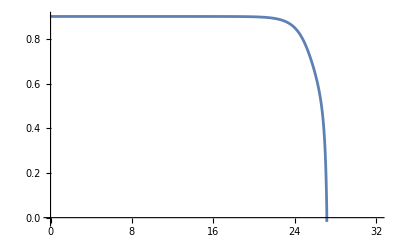

Minimum objective function = 7.897875

```mathematica
Pe = 8;
ρL=0.9;
ρG=0.1;
dϕdx=0.00001;
d2ϕdx2=0.00001;
s=Quiet[solutionAndObjFn[1/2,Pe,ρL,ρG,dϕdx,d2ϕdx2]];
Plot[s[[1]],{x,0,s[[2]]+5.5}]
Print["Minimum objective function = ",SetPrecision[s[[3]],8]];
Clear[Pe,ρL,ρG,dϕdx,d2ϕdx2];
```

```mathematica
Example - (close to a solution)
```

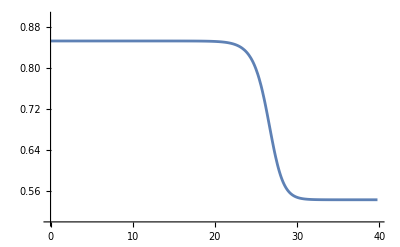

Minimum objective function = 8.0346597×10^-15

```mathematica
Pe = 6.155;
ρL=0.85225822768627697731240972743267519842105356617866091747517958120261044465764`55.;
ρG=0.5430846492028957345330610070945616547047112435171140384821038994376621249119`55.;
dϕdx=0.12504741303265277135837042339192911409842798982071056432008142206948608607309`55.;
d2ϕdx2=0.01683435082631029058606745249621584005940778246599234478836222337589566188414`55.;
s=Quiet[solutionAndObjFn[1/2,Pe,ρL,ρG,dϕdx,d2ϕdx2]];
Plot[s[[1]],{x,0,s[[2]]},PlotRange->{0.5,0.9}]
Print["Minimum objective function = ",SetPrecision[s[[3]],8]];
Clear[Pe,ρL,ρG,dϕdx,d2ϕdx2];
```

```mathematica
Single shot optimisation example - optimise parameters by minimising objective function
```

```mathematica
(*"
	known approximate solution {Pe, ρL, ρG, dϕdx, d2ϕdx2, objFnVal} = {6.15500000000000000000000000000000000000000000000000000000000000000000000000003`55.,0.85225822768627697731240972743267519842105356617866091747517958120261044465764`55.,0.5430846492028957345330610070945616547047112435171140384821038994376621249119`55.,0.12504741303265277135837042339192911409842798982071056432008142206948608607309`55.,0.01683435082631029058606745249621584005940778246599234478836222337589566188414`55.,8.03470156979471325041752338399580621284525108622345186865839499`50.*^-15}

	We use these parameters as a starting guess for a nearby optimisation at a slightly smaller value of Pe
"*)

parametersInitial= {0.85225822768627697731240972743267519842105356617866091747517958120261044465764`55.,0.5430846492028957345330610070945616547047112435171140384821038994376621249119`55.,0.12504741303265277135837042339192911409842798982071056432008142206948608607309`55.,0.01683435082631029058606745249621584005940778246599234478836222337589566188414`55.};

(*"
	Set up lists of objective function and parameter values
"*)

objFnValsEval={};objFnValsStep={};parameters={};

(*"
	Use a value of Pe a small deviation away from known solution
"*)

dP=0.005;
Pe = 6.155-dP;

(*"
	Set initial parameters using known nearby solution (i.e. for Pe = 6.155)
"*)

ρLStart=parametersInitial[[1]];
ρGStart=parametersInitial[[2]];
dϕdxStart=parametersInitial[[3]];
d2ϕdx2Start=parametersInitial[[4]];


(*"
	Dynamic output of optimisation - expect convergence after ~1000 objective function evaluations
"*)

Print["Objective function against number of objective function calls:"]
Dynamic[Labeled[ListLogPlot[objFnValsEval,PlotRange->Automatic],Last[objFnValsEval]]]
Print["Parameters corresponding to minimum objective function found = "]
Dynamic[parameters[[Position[objFnValsEval,Min[objFnValsEval]][[1]][[1]]]]]
Print["Minimum objective function found = "]
Dynamic[Min[objFnValsEval]]
Print["Number of objective function evaluations = "]
Dynamic[Length[objFnValsEval]]

(*"
	Perform the optimisation, starting a small deviation in Pe from known solution
"*)

Quiet[FindMinimum[{objFnVal=objectiveFn[1/2,SetPrecision[Pe,55],SetPrecision[ρL,55],SetPrecision[ρG,55],SetPrecision[dϕdx,55],SetPrecision[d2ϕdx2,55]]},{{ρL,ρLStart},{ρG,ρGStart},{dϕdx,dϕdxStart},{d2ϕdx2,d2ϕdx2Start}},Method->(*"PrincipalAxis"*)"QuasiNewton"(*"ConjugateGradient"*),StepMonitor:>(AppendTo[objFnValsStep,objFnVal];),EvaluationMonitor:>(AppendTo[objFnValsEval,objFnVal];
AppendTo[parameters,{SetPrecision[ρL,55],SetPrecision[ρG,55],SetPrecision[dϕdx,55],SetPrecision[d2ϕdx2,55]}]),WorkingPrecision->55,PrecisionGoal->8,AccuracyGoal->8]];
```

Objective function against number of objective function calls:

Parameters corresponding to minimum objective function found =

Minimum objective function found =

Number of objective function evaluations =

$Aborted

```mathematica
Shooting solution and objective function for initial search parameters of optimisation
```

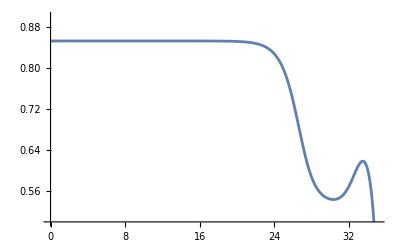

Minimum objective function = 0.00016368868

```mathematica
Pe = 6.155-dP;
ρL=parametersInitial[[1]];
ρG=parametersInitial[[2]];
dϕdx=parametersInitial[[3]];
d2ϕdx2=parametersInitial[[4]];
s=Quiet[solutionAndObjFn[1/2,Pe,ρL,ρG,dϕdx,d2ϕdx2]];
Plot[s[[1]],{x,0,s[[2]]+5},PlotRange->{0.5,0.9}]
Print["Minimum objective function = ",SetPrecision[s[[3]],8]];
Clear[Pe,ρL,ρG,dϕdx,d2ϕdx2];
```

```mathematica
Shooting solution and objective function for optimised search parameters
```

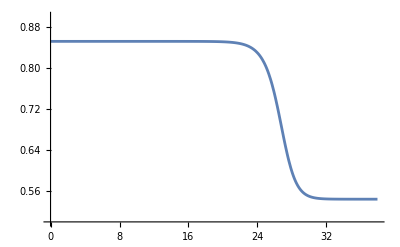

Minimum objective function = 2.5824259×10^-12

```mathematica
parametersOptimised=parameters[[Position[objFnValsEval,Min[objFnValsEval]][[1]][[1]]]];
Pe = 6.155-dP;
ρL=parametersOptimised[[1]];
ρG=parametersOptimised[[2]];
dϕdx=parametersOptimised[[3]];
d2ϕdx2=parametersOptimised[[4]];
s=Quiet[solutionAndObjFn[1/2,Pe,ρL,ρG,dϕdx,d2ϕdx2]];
Plot[s[[1]],{x,0,s[[2]]},PlotRange->{0.5,0.9}]
Print["Minimum objective function = ",SetPrecision[s[[3]],8]];
Clear[Pe,ρL,ρG,dϕdx,d2ϕdx2];
```

```mathematica
Data found through above optimisation-list of tuples in format {Pe,ρL,ρG,dϕdx,d2ϕdx2,objFn}- for β=1/2
```

```mathematica
data={{6.40000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.88205682157105736309531086157991222087814686501836627261560797993927030200384`55.,0.49563482692809425830162729478897220757847105674672101727260979674043978687402`55.,0.12504743141722530178190547969193736996087793853612881814429051423673023873269`55.,0.01683431700064124510525870470139789101624107180575956036530151041712328152272`55.,1.93000422219587122025589378742670345933877415749202088931247614878`50.*^-12},{6.395`55.,0.88155715127782345573245456575480223221932482000060562402515588125082307645751`55.,0.49648029965577229602146385699910154515840652328156502381182335647125902686879`55.,0.1250474315195967703468728703182558562402069153611352399815309557499221408717`55.,0.01683431703620624342934864607582311996575901037118216943246610391972582388279`55.,2.28941674451896187327078177759694494246928324475671615364874128646242`50.*^-9},{6.39000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.88105372555970553202297987204569545792146317085468358223494215820856430734661`55.,0.49733001905017131586663535900122155554558385744287513461834061822155033522856`55.,0.12504743460055856131584314943005924446435481494117451034264653053102471907848`55.,0.01683431700997879334556450633897140324683827845491428239897989536107017883745`55.,2.1121075023274977953689580418287457808794815595109210378326692245455`50.*^-10},{6.38500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.88054673224481816381777179566293150236103068522276217817431529843391115763013`55.,0.49818392011352438333303817909939829836675819996443684212328506595136511477358`55.,0.12504743464118541202855794370461333684919983607615467824940558197837408997415`55.,0.01683431650493870184424403334258475878530943639658463272115568337272120645101`55.,2.3676933833160433809904323341867164810893637437393800568794351969139`50.*^-10},{6.38`55.,0.880036066414765478599812714859758833164689976556589719322109454859161319826`55.,0.49904207823632616504090337227324401007725258972214331118961290901891950069035`55.,0.12504743465048072555355691964186020839206181743409440374194043180343234444002`55.,0.01683431674313873691685809469003448282917335780629498378487886446708851221384`55.,2.8685479445511180261446473660284602996541402892030323658467167103437`50.*^-10},{6.37500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87952170687129066703421232436901272078018592399468149152825200150587642147039`55.,0.49990452509636439996319711934016595507703814607557722982253458181977721416584`55.,0.12504743448749190790609179569923845443279295372815489397267628634667535861448`55.,0.01683431589797734176026794850045944515745303444644965769450291979453306340001`55.,6.0857775230180063430129582783088961749026097912160295033368500250864`50.*^-10},{6.37000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87900346732551878200304250887628312321742083886418258038235110286291024933866`55.,0.50077139976203530120788495532493841421938442978335459227662449148765982383521`55.,0.12504740848620089155838940409165289291658464579116095092599460919571402229907`55.,0.01683428944167181236915735682924281636927721591466493132524006067579792023015`55.,4.270988667448465070191181916807882208519466288126576059662157131925`50.*^-11},{6.365`55.,0.87848148193811023078623756698826340515778292847443716732510533362591540964178`55.,0.50164263502170101928832737431256807705313244117760827098289509884759738663793`55.,0.12504741113211061328432482840505595047188340687334967567837970763485707381222`55.,0.01683429159302893472367374966179770844371785311022100682128976993183835805467`55.,3.354869240154760829309773766483182189651679018825597497240084424985`50.*^-11},{6.36,0.87795564647998961923049693879769646225346294965488424645263569217722036917755`55.,0.50251831462487808793760456594815526558554033455314449894964827002565322510626`55.,0.12504741113286629345851291216860358862747904248015842595817631957075203046086`55.,0.01683429159446880284145848795991083974662210398115032296785059043680912246218`55.,1.4805847193273728415433726724653147242988066258106828152060910878392`50.*^-10},{6.35500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87742584881168672658406458360469704665744045720039425509856385119271011954534`55.,0.50339853666040860768897510889801929011904577143328913124243399649525979675453`55.,0.12504741091605844703164453046317177919058748078592495321017174590682050556234`55.,0.01683429831380600406233076609282358773091337384020831125090319280481328055978`55.,1.5923585017318651137633790200453715865173073010981585166985145944`50.*^-13},{6.35`55.,0.87689210382499169976969998789179100560205187381803374078594277091527105319175`55.,0.50428330444436822714506297836095700891437294290778291018054600562407067173833`55.,0.12504741519616135910939213679741401391773728554835152904020192280198121033257`55.,0.01683429578074151076408831389660821147339208167912328365764581705999445398958`55.,3.850856941247347711642784616465958172674108301828166451383813387`50.*^-13},{6.345`55.,0.87635433321551825433325466398456645455675442395566632222071922194727937863256`55.,0.50517269130103532598228761405656224115868042894056849594510144328910820118981`55.,0.12504741059648313716520940194293863977456131587654031276743252447865227087192`55.,0.01683429155714722429003019233141342716648051609245111589629396936405680318638`55.,1.37866413345210100342107576789099992604244255035695907118036158781`50.*^-12},{6.34,0.87581248626912430160429596211123623575727165862576257578319967450016116965532`55.,0.50606674964805888326907271001866007035166218002073546707411588422243980265788`55.,0.1250474106593463068517142482398736523987833043511470990339651868174333650233`55.,0.01683429157943360224338037308292711906460414588651235100208742987981199790049`55.,2.76229791304778897222523035496383705878618237299681880660854876961`50.*^-11},{6.335`55.,0.87526649459555672128335290131399262493882172707009436285446053952322779394146`55.,0.50696554839985072070337548542589358275840660607329916155156170280489632946366`55.,0.12504741432341638071875130273596922782217787544306289702969326366306080242252`55.,0.01683435284131976996662622478648727901974511858434777477129106122172456305626`55.,1.26939075574470954214482378195608759045665360869393406026258414309`50.*^-12},{6.33`55.,0.87471631529204476121435226696376403790688628043750390367237268470106285214784`55.,0.50786913291173051538540974116028251422441663859599154660673831610838543260536`55.,0.12504741065934631326746267972309358407565286138346655940608579751376017801563`55.,0.01683429157943360763263367593036346376191917122446723931217602106342674444699`55.,6.5662736247356280472916956638968083102721941194183302542829234787`50.*^-13},{6.325`55.,0.87416188521776765066294177228631102472666244776258312173361266467209769968256`55.,0.5087775674341839530078682494957976508498263943356889388490515077920875295805`55.,0.12504741421557804026049720460950462128040271474197278747996962887005432842997`55.,0.01683435276403531402612620508182134373246320803057740029705660869237242412203`55.,1.6117170577323470427765503389723689379459034502937433275888576231`50.*^-13},{6.32,0.87360314923227751088354807324885421318933370521064486326376127360564736028308`55.,0.50969090779989992233113158503810439447574464398164568526440598805842983950788`55.,0.12504741421517552843111787009819440660954477607924066477131496769284557908016`55.,0.01683435276413897546592637467359144744880072779960343929776956019064908624892`55.,5.260825232409004315053692136505509989701919984095399873803323502746`50.*^-11},{6.315`55.,0.87304003427209171585679592025205647930367330231408729359157627246764060888208`55.,0.51060923085937550335533178797078722878957410401844808927890171157248640996176`55.,0.12504741463014181380982379158110420275647981011063279570293259011201679066762`55.,0.01683435323374413000100724818709795468438801938977256310409219027351618288432`55.,3.423954447669374562623429362583548481297182808016953371670383417`50.*^-14},{6.31`55.,0.87247249066006910557248636480745650944891070615094226605412711348255005213949`55.,0.51153258543728255138580262274811255124621931880368643511743983989161121387764`55.,0.12504741462975456607998340668934060145764386344094113184756592457283701757242`55.,0.01683435323324615444356150209322035852094343720276998600730348129548605673463`55.,2.13816548666732136962508192716234700684958087467004347385748428`50.*^-15},{6.30500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87190045087907098100843159660585360623971424806843715019332310231415233205451`55.,0.51246104118730055465039186209786514819861360339924003092089930759474738413242`55.,0.12504741462886142109067954865341470778278803254771781653494612981435645528339`55.,0.01683435323170061889872471624207732333255110931860298652445442843994192068017`55.,2.6098168269777078510810043088315452189243434918001099437085660556`50.*^-12},{6.30000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87132384947679807046780011426263719127211465637929573705803396997913869136247`55.,0.51339466537907941134073102810512354073104511120492594978665432228485935592946`55.,0.12504741464556523172664976539306762078961410001125537210488317581336199685904`55.,0.01683435320613129779356972870116722659554663318112220444126563743389489904453`55.,1.785768829273764676744346106188389396725132870616520852535316237`50.*^-14},{6.29500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.87074262036277645291878121087700764557788179075712196853283284289231365764797`55.,0.51433352525706102984291469340977915957641149341399777769482856862811344784325`55.,0.12504741464472173943181095789495367888613772069230649929820053550416930234162`55.,0.01683435320727531237831837861477049775598311767681303143538681270466007097278`55.,1.962401164010249211522167086689424245434454763264772672203300722`50.*^-14},{6.29`55.,0.87015669528231653528749331598002030422346232289668424262019762917437942982629`55.,0.51527769067856053064918166827126025649314348117186753892945818339759578341039`55.,0.12504741463779474332752389619699445562806218352769168112732445872244303595791`55.,0.01683435320036646076116468611006690471673086137109754383873672810477599362126`55.,1.20683483319490101608658038521373063331681305675060535059046333`50.*^-14},{6.285`55.,0.86956600448879517785375202198241321943010128065521672069281941897513314503229`55.,0.51622723288420557671757102508151698304891442833229492945173786254646831083713`55.,0.12504741463055055165123751592476723438264608552523964209058994820927755380399`55.,0.01683435319272764230234905274347628608453380158192975032216264704698151446546`55.,1.675902244400744736761329525455491279637344346839501476206476184`50.*^-14},{6.28000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86897047655165076006647086826112730844095235930415786534879598854731963757501`55.,0.51718222480598197755943646830488193141582130287388756066734932539653961972803`55.,0.12504741463307622763205193881623969015824893417899400936594203037210046012336`55.,0.0168343531952602900684129297363371993125039432249024783484163754522039396702`55.,1.557218043233245451574454516165942603568643900258926014751957416`50.*^-14},{6.27500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86837003741182503927843251030348206528934173025494950789278888377641227644915`55.,0.5181427416163370263031749798011816562990157536606230868229838320723443883728`55.,0.12504741466472170931266156433311795731898732888860894531415663794393272807106`55.,0.01683435322691924396143890097487939466418968291874072414968787511324858135506`55.,3.427327559373113685296949298943542645275393648834714502678595058425`50.*^-11},{6.27`55.,0.86776461471530050633170666123898531638962269692067510297811159703376333961753`55.,0.51910885835339475684137888105437511670034120206798671304760013286278017197151`55.,0.12504741466319718444146208956061019711152822813307546649163626414718869827204`55.,0.01683435322538027208494463861744131329447262424869493895339896823522479487398`55.,1.162415973144450153354643899503761369961973792310275072233466674`50.*^-14},{6.265`55.,0.86715412896831894745332485289399217703121748144618846290708159538664681258682`55.,0.52008065485345520979771021191789635968850751797750840956559055744338569544005`55.,0.12504741456266892708162618105930500955262811988890378068005201562413488035971`55.,0.01683435312486489190460399834433414892609267395479224373217111033307046738232`55.,1.826799835073622398738870020258948807117934013703262480032875677`50.*^-14},{6.26`55.,0.86653850224593085969445906183891135981256497766757750690973579017625930555005`55.,0.52105821095147759404239210197893393032173580861500334426495321482590707580915`55.,0.1250474145659210892444545818409203437718791164775040714124077537864344870873`55.,0.0168343531281377499258170733864105154100492138453338906210544320954703462952`55.,4.765184419556869695649063145672818244445578925888434062873309663`50.*^-14},{6.255`55.,0.86591765375724074746474320229061078044306485987549592247428790439741381737926`55.,0.5220416089624038235779158889886637498624123023338750025692821664101623653715`55.,0.1250474145735490252402001543240659689030667177499210933072809635199816460955`55.,0.0168343531281822691336488439330095517127302343937383327079404235849002787354`55.,1.207997715102811201033955988991633648353860048455480441836444833`50.*^-14},{6.25`55.,0.86529149960013897711822876721138126672828492399372197607145476556261045649355`55.,0.52303093423564799795072304967916467799829329912337365451886738764808002772796`55.,0.1250474145764804104539772198247712214675799162465234227593113803520373855425`55.,0.01683435313309871645798629816965675142486523713204470880234030649699376885539`55.,1.700618583077630414434356870728747427387646733674127329997961587187`50.*^-11},{6.24500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86465995772931294918197900071216794615132533579820374499317910796712876608307`55.,0.52402627060304564124801849239321173552539115031136484990781171747773641804398`55.,0.12504741457739025962148996837836996325240120012704981654774077338029158546667`55.,0.01683435313281620726708311026988479192146202870786139867991142791799372759042`55.,7.32807782004607375869766127792680176362548040338323880331946708`50.*^-15},{6.24`55.,0.86402292702373028879090534068024475654573931341701587266204689317701362787942`55.,0.5250277190694977251915884339683154797193383827459275356026206920793376192553`55.,0.125047414577290235585676048361882931295646248256074112501897917226214268522`55.,0.01683435313274945497398914541697400936825647954712538688605321017637956088201`55.,3.2534045253379680553511967947205312582635070650787935894780405402508`50.*^-10},{6.235`55.,0.86338035139805169398682490659769195800049392237647947391344993518694494732853`55.,0.5260353415622524849694874657561396244766749035008242823571150585262492334487`55.,0.12504741452651266618654322809138089350040680252609771003037905187182656864612`55.,0.01683435313266878761009624394914454998180398426450054443345508016385100128824`55.,1.56691088568389512065914496207159315221110203704343513426515969`50.*^-14},{6.23000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86273210631230507702592401939579885158038479737062372122659903313308740091581`55.,0.52704925995593608866806710102378888081813681332496422866692542211463868727735`55.,0.12504741452933842109630236790830768016831653506735265759586507366357923921061`55.,0.01683435313278319728178960944934662451312320964554926081146845244722363968475`55.,1.138653158430392727438798648186363755495828635561737769278667128`50.*^-14},{6.22500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86207810808943879744931816025519143375203546130797991710771096122344589384178`55.,0.52806956088939577746427599806798863970101382301707247998980337453032629131285`55.,0.12504741464165089054410447437633646191591891333703472398031155073843285864673`55.,0.01683435324590595029650436240465982364714054989194783403602937480425128399843`55.,1.991569243125013021689506990632610790471031632049019272593674278`50.*^-14},{6.22000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86141825960560262371095291519448494891967008347897158596519481264871334072704`55.,0.52909634304427653201186245417483497226514815136507699293031945279478854193767`55.,0.12504741464394288241260496149367440469581922661924410858458326717549569451805`55.,0.01683435324817958022601088325680222702744524433572059705258528331440912612982`55.,1.943962267421924448919654311872768496239914141878852479458552624`50.*^-14},{6.21500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.86075246103734245428587731661118546909135097468115008789185020030387988230021`55.,0.53012970780781015866269025463687377332955006752349869547603907108886268191171`55.,0.12504741463868767682671474056027823395337561653165211933997390314839807104831`55.,0.01683435324926336496042537015943933705098655996881664613649638852176248795587`55.,1.476679256485013846353222834859612688175183870220211873227445988`50.*^-14},{6.21`55.,0.86008060975339674076271793091245863269450474119758539590036327214199598715753`55.,0.53116975938506410584435898522049339836443666124187656818339969772256211952371`55.,0.12504741471432324470801352276606090840572206960874560485383627448347300807096`55.,0.01683435324806768011556242412159546266882126630047462485529490880344460330569`55.,7.46614236763298868985345078104276051790504911410398497919414615`50.*^-15},{6.20500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.85940260019542421251758126732418492040361253273480609086631733051696023724282`55.,0.53221660490887235266271289010192022611010264385048935499009362834437067636575`55.,0.12504741480856323806579489011412659374667396913844945300297981085546873006432`55.,0.01683435328238254220072308401397339978805280547071462006793911872640822167738`55.,1.897341583336456214125328326987567698411358469654437426632825366`50.*^-14},{6.20000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.85871832375999619472172839892334952783015406636384856297643944647919147145434`55.,0.53327035455909306860207396867367167896594189414028182117421638499953393334714`55.,0.12504741480828354626353776372560693052213247903370075691429851185964872584162`55.,0.01683435328242651940687911252755311633933071654981279353418464483607864903779`55.,1.470243194437290746526586724068407690809202278435948175107155389`50.*^-14},{6.195`55.,0.85802766868473807656554688344435174637867857158686989145561732900943001824419`55.,0.53433112168719085310569696579458721022931521733799760755752596923918259213664`55.,0.12504741480817545152533625167004042036061661350064210948746636267542852130941`55.,0.01683435328370269282493144408417254543968553890864445264173896229909059208076`55.,5.26947378169582571147822577876453187650941568772834257601607097`50.*^-15},{6.19`55.,0.8573305199008949776209821334558297292446975416861477366890639256417476411219`55.,0.53539902295151662862320314782945714742310297051825527466608431852147956346539`55.,0.12504741489933000551599877962417267678783854295278315883701119956497985725882`55.,0.0168343533761736480002271870577473375752898971078517751220209923650927648948`55.,1.501960594891639204392980281294248744305549262742331412676884287`50.*^-14},{6.185`55.,0.85662675889362428946098241034812890813665223962621053794783568103069407819401`55.,0.53647417846233444958923752377103486858939652133121522179477446355285827429384`55.,0.12504741490510654151337197969841745277747164634394497555371365403921237705203`55.,0.01683435339233582271691944321493003528471667562874111632432935176142849993889`55.,1.185973021276149305865579993470751699146147617462868946748078214`50.*^-14},{6.18000000000000000000000000000000000000000000000000000000000000000000000000004`55.,0.85591626358142353775775081831377690621565464487334574909767154497221354959876`55.,0.53755671190245118336152497725430357814848526490602563759045345291437157873532`55.,0.12504741490503991513868094575200948446237665820245578033149887870823964043111`55.,0.0168343533390611214560223547404930356277516423223125769966909451211203441335`55.,9.77620574691352009068697754494422333484064483287594581730092043`50.*^-15},{6.17500000000000000000000000000000000000000000000000000000000000000000000000004`55.,0.85519890812248612987028706116601399462075965071871604867025798756203343201989`55.,0.53864675071943162406133494505509090894439065954424150951657156597526711123794`55.,0.1250474149052403007490051693745924118653227347929832441493950762973088761723`55.,0.0168343533390170609397609481640580712734715250742604975615737309996524631778`55.,1.922573355445314416071504973100802311215546363784948498575567252`50.*^-14},{6.17000000000000000000000000000000000000000000000000000000000000000000000000003`55.,0.85447456277282807417403840341995407133529649016081560124195136182963453424529`55.,0.53974442627010802109619605199255220542345732005265558411606164988582099566569`55.,0.12504741490528942354260812227141935075412132397384458627658657445581564356197`55.,0.01683435333902938494018935260229455391528900606734593841404273880007424931913`55.,1.875492761302666928609702880004761435492759098117715645377064873`50.*^-14},{6.16500000000000000000000000000000000000000000000000000000000000000000000000003`55.,0.85374309371501499541267764151220698883355036116049378648745251004025256818401`55.,0.54084987398749412833680121252326529537294933295060755180057938451875356681442`55.,0.12504741491046674031816926558983397351299288600405107762912266961343647072935`55.,0.01683435334704153759906325605148193935313993908402786618227764220427900199039`55.,1.867324214399799987745209297246891262592319826906121752549900858`50.*^-14},{6.16000000000000000000000000000000000000000000000000000000000000000000000000003`55.,0.8530043628655531879022943775370089487920335324281667084776768990405680662506`55.,0.54196323357584047180565598838815901883847089389963707058574451593096835066682`55.,0.12504741491116752766222010959140073465939405371605276511871490427768796549817`55.,0.01683435333273314285886987229717864711331454238186121015341270123115306554764`55.,6.35259661128434276529025499614094393404515238825639444536428745`50.*^-15},{6.15500000000000000000000000000000000000000000000000000000000000000000000000003`55.,0.85225822768627697731240972743267519842105356617866091747517958120261044465764`55.,0.5430846492028957345330610070945616547047112435171140384821038994376621249119`55.,0.12504741303265277135837042339192911409842798982071056432008142206948608607309`55.,0.01683435082631029058606745249621584005940778246599234478836222337589566188414`55.,8.03470156979471325041752338399580621284525108622345186865839499`50.*^-15},{6.15000000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.85150454096978895196944437141052724744692209309745671286927212158632091458357`55.,0.54421426970861358187357494195662399472442684609533702676280721953760264744057`55.,0.12504741303236719233219230164181229996034371804998853900600266655135514881863`55.,0.01683435082617647760403620449052900386536753509957259808933366951754911765325`55.,1.046755610853515092676818992791042493449225576637101940217254186`50.*^-14},{6.14500000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.85074315143066330042046018395972294710108051781140661493262088454528169444939`55.,0.54535224809359017990881457581148761059252090076865843707564740390642144573339`55.,0.12504741303298198830839352252665319253997340367223545028528017997043802755538`55.,0.01683435110437411084940027044012436637802410917241142734931332078129091200296`55.,1.099249812946946282939450446335156964438624781964558437591604797487`50.*^-11},{6.14000000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.8499738994666811157756180879307669978816852751548375111672405372549084451323`55.,0.54649874537123910792302420393166342753351803045757605886994296346641323651`55.,0.12504741335011860724261100913400215414826310812220523302422032380822294366089`55.,0.01683435112585418715368032719026370849136856772868855871750865575779462134508`55.,1.201330246482302117334979774061568371839092744998827459649923914`50.*^-14},{6.13500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.84919662491811745335282552625085730566024995048075514534034881395474116583144`55.,0.54765392356117187001217294956493500863662155592716206741860239329892949997325`55.,0.12504741342546375803838065236234917050044152129311064462994403396099718022631`55.,0.01683435120176394322768853750734521547616650881273787405023826309860950596045`55.,4.7120310818965748949105171441122841951210951608348708007292244769`50.*^-13},{6.13000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.84841115881657245021739196413797964841033036694821733114652116586171621423769`55.,0.54881795327471305962858018620209073044811484006465162493766803833366936318636`55.,0.1250474133741283909550133494168751604745002117864485245995470550740117445832`55.,0.0168343511504408134607639653375308050838462425975973643179798943556148252782`55.,8.23575574909037913951513894065497137662675969631840104047584103`50.*^-15},{6.12500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.84761732709144997214593808780073960558233379705529207813387782851961580224151`55.,0.54999101004993634953292507264441455686435374151872084703064268900883559944608`55.,0.12504741337604000769862798446503746169445142145757115783086759452682416064639`55.,0.01683435116061570959737875018846535370890718216536109428871847501392129449625`55.,2.8416724087346529737741000524800252915045814627980343628683621388`50.*^-12},{6.12000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.84681494834254762895989168803146593476796886328097743475551638828164496159552`55.,0.55117327678249482554344536751099627087459804161512126534232788160311423237755`55.,0.12504741337584920006448345929303683628160052779986359902488722193879694229935`55.,0.01683435116041374276761633130034650749570223735550227645652483354527322638163`55.,4.986200155372756192041855155972018105450637070816056529036742843925`50.*^-11},{6.115`55.,0.84600383899217905302944516741785974914078438394222796256480241440398660501948`55.,0.55236494004669936770999643865870759956891765746212207659098283938522867000336`55.,0.12504741296001722794043518623894091507437515755283062135208325520442191230347`55.,0.0168343507684042317530265723464873165656507015160437581872027562474157957532`55.,1.448559166152031468303394047171567274636250239344725129518539013`50.*^-14},{6.11`55.,0.84518380223922393772179922175448380694847471581845942260450672806761388037395`55.,0.55356619674398093403846721614182750541952852521309529201022600141099961199219`55.,0.12504741289487051921179640510257283346842056140381216014704175551202364839125`55.,0.01683435074325279689513937875464524220207473404490462540635780396439166123087`55.,7.9700726972497197778684884445467647053427216774263053540442998`50.*^-15},{6.10500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.84435463827414144714466077129091993282545858580519022288611424876128375532471`55.,0.55477724893490791947666189313544936131032632787803988575233734397430918804062`55.,0.12504741298096620757713118235209411531507902756379025525328168452716621524954`55.,0.01683435116243677973384859090689895270529835386793288402603568427909006522805`55.,2.39731241176403662964326233949956947282700155400807469234811883`50.*^-15},{6.1`55.,0.84351613864359209065613115825727872118590289244396030074413161475549148983893`55.,0.55599830675746643497731996416452992071371281966376064507520476635881611790194`55.,0.12504741301039385894754282441335193905258829822616422446772261293215174249187`55.,0.01683435135198444047856319207166111116611295543040547252259355157705550510443`55.,1.425471523414588121458102635037195022547897784970273140456882777`50.*^-14},{6.095`55.,0.84266808688835703145718331891097347222965514289774136664896758008726518576968`55.,0.55722958836859957955673828476860558543982844597723526271963446122517316369925`55.,0.12504741299763770399888647745453947085636353715263810604379415656778873869003`55.,0.01683435163900215481559164007323793270286669722348897253574419750456241570993`55.,1.792148637013216711812161688134314442945704911942280685227794698`50.*^-14},{6.09000000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.84181023494543411276327054761504734846415922879796507171862732685641786941969`55.,0.55847134707061819192541554250793808846043608835400873115653845728085476398369`55.,0.12504741268946190090044636719323944947173040462212424015529426755972859256712`55.,0.01683435148984623736359869835586003466537202466981532571825869464794613203293`55.,8.7208197673410045228218550885811996287534510878773056312818246634427`50.*^-10},{6.08500000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.84094241847169051494806975536722766079226660007893303107449982105158565755879`55.,0.5597237382725380035396725771634008643920686591909900500395320846568558875142`55.,0.12504741268973087777276121259893358879594705082551094224340274337819674479638`55.,0.0168343514870249744326702934007520705297029308506508640261363280997567067527`55.,9.81679951612862628556116014247376333253300415514014727378784886`50.*^-15},{6.08000000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.84006432471221141374890530889354387513698903175387365329523092562640348175282`55.,0.56098708708257279848126916174332886207546138367538795812623975864330459320235`55.,0.12504741316406158700035287978562946885566964292895624586527441377974750703456`55.,0.01683435120688627789627986915962245917078218174547973771967989641450573091839`55.,3.68167691804679936245358137765931479267915531670138471619047726`50.*^-15},{6.07500000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.83917572359732667654094158192941357114345027220674176566799067321100815406157`55.,0.56226162173763556865832189692646408664547585350015313767978086374817605195838`55.,0.12504741312755150043387454544300463090323147229168674006517370067785365753779`55.,0.01683435053317781181976438734210212077212078305904998692589259177872006046534`55.,1.564644347244346354634895074704358155960620336728563322805131934`50.*^-14},{6.07000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.838276351322465487860602781657820113927829217954895316023208925505883206408`55.,0.56354760776010103807502071805532117229432159200975876357606109517361147789019`55.,0.12504741334707141946523837946108742567341901389370502876418848823286713187139`55.,0.01683435043824274052912666651491624031492882119041256910501722917566590028216`55.,1.020975659091351385899740086970799704744961988740184257218976028`50.*^-14},{6.06500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.83736593288634416313302280711398862112058364828224417482592072730491416950429`55.,0.5648453218819549134358205643616352550576460565339909819905996829227634190413`55.,0.12504741337299365008883733110864337018872692754513447315866826245488011376385`55.,0.01683435128772168155345232631744739980065664432894801270030181284825949229072`55.,9.3746510338536362756324835214584604646194102802900264852666719`50.*^-15},{6.06000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.83644418141667915395584998061656676455106697597711088737556768814254175839971`55.,0.56615505270772264747910457462708179788602915289649198578320425547615879994336`55.,0.12504741318557043330016460772842227443325300330643074770498721948604582860233`55.,0.01683435041370082443411971562932708476569502565512273938106502236144503751066`55.,1.785440220699941715596044704756192504714436990655422060375744051`50.*^-14},{6.055`55.,0.83551079741434856380369395585769848795695168733730245073804363051444922990836`55.,0.56747710147988602830737308276618001245970079456842556031906884926987782096396`55.,0.12504741378854585407006625271522566362513408852552241413300976072887700589035`55.,0.01683435102287232633490570143499573397355290676862124184315323454196960249909`55.,1.781965136821115960714849865423772141990028143930058566009333415`50.*^-14},{6.05`55.,0.83456546821206558296069281283479542845706028811767923995763393114279195425066`55.,0.56881178269691527809334312032618190953352275802689041734226891781425313359001`55.,0.12504741378808698464302892293649492625523347881449858645980004338231064451185`55.,0.01683435101367394595176948420072857059122379339715895180126188788891940424484`55.,4.90864673893768388330517222806565029004776975107810749273248360823`50.*^-12},{6.045`55.,0.83360786765573835699459854208085020693213084747550716507296281034952202914246`55.,0.57015942236804770721948574138190056290668524596511642192351309018363028594891`55.,0.12504741378840264504012365463754572620231239321932215405863366922860390480991`55.,0.01683434912694660413509410595595743074123917847260316319992801295132922226421`55.,3.663937408211203783166171074426831478745136763680364405846582987063`50.*^-11},{6.04`55.,0.8326376487778256348867374737558968728739078191263045090345509107269029556729`55.,0.57152037433677378242057757828613462606628263262772306663263618653564221660997`55.,0.12504741431968669174076158910606466685615478937961780034656619582297153172197`55.,0.01683434912907417216462342553878242519409927638564836245541228102644840544983`55.,1.300572725983468442162816831199821531968190919737041583455373078`50.*^-14},{6.035`55.,0.83165445799859557341136495592448588954433337766359458171069740821882115977469`55.,0.57289498902017240005461165189177148051492212081024384542243205467025643752181`55.,0.12504741398946029207421528898910011078787558447083997935031233052877464381063`55.,0.01683434880047644757099024709780037720536365156123464426791004102923586600085`55.,1.542466585267529530329382703615659445921622658750505644000005834`50.*^-14},{6.03`55.,0.83065791756804172730998476924463970710067997808097188493718215293828469584236`55.,0.57428364754445033371074813453728597148592695529951350268244727382998096567882`55.,0.12504741411956146931855545165106960471783556507889646043292799515931455215795`55.,0.01683441648031549797997228122676052090392966304165770048099847860605119316596`55.,1.497573220542263736720135780872897241754022126331375903013410003`50.*^-14},{6.025`55.,0.82964763296835318422420615358828535700375928848399186763323274229006550684098`55.,0.57568674619996815314840058267773426143233643735298166486779698934224083372197`55.,0.12504741444191481202026019973631742800387991983458875752873581790927229071359`55.,0.01683443035285880516124392704139245838088881972730456436679869996884042786127`55.,1.914222801999835540785477706607700933229188689775455253608831805`50.*^-14},{6.02000000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.82862318940932579554800652790466012722119868542909085900071123990630908899798`55.,0.57710470161852471530303637819400165346001068266497479489603880846077613733351`55.,0.12504741695414820203415512082680849492894886579713953102745031528016891810948`55.,0.01683443274045435070065704135810643871579047064522744071259434201164084713094`55.,2.53413181513362787616394656065525483707665452715347381439984572541`50.*^-12},{6.01500000000000000000000000000000000000000000000000000000000000000000000000002`55.,0.82758415241655942116456715782654266398864287262527426469787852238541306388718`55.,0.57853794988436605598599263654713378135902468637764869915323053347614014223802`55.,0.12504741879004423728135620888428748131324538040096633176765714012605364222624`55.,0.01683443445931167112171425835085624310520089246651781266913791737332801241333`55.,1.685238737787947836102293837044444487905512710367614760892970646`50.*^-14},{6.01000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.82653006220642855037960848678506030833024722186333385464982234849674416242259`55.,0.57998695274290931305218204648836298607286236591064686292378931766607296783586`55.,0.12504741875784534102328529955253696784124692055752996150948606165312236496711`55.,0.01683443442804570702830638232726271515945726919294118624928396422974967361421`55.,3.02755758655626493575588944704274552478089425662302430593814412`50.*^-15},{6.00500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.82546043601454704334865020848697092994235512804065900939664639290085151681318`55.,0.5814521946987169341029674548602700027506508907685576333555438644230843420338`55.,0.12504741872003174415828366352403366348977126143434952176061036071520012875086`55.,0.01683443439870268468485951525791259188748337580175257778213911305996821165421`55.,1.912796398990071328269153516915308272376167824901830640750586554`50.*^-14},{6.00000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.82437476433631104445463427472990908646354464674924308568178428891378117802285`55.,0.5829341869136597220684853128338380267361680082718774888384018524164780282135`55.,0.12504741870195804917921606562156808855920628294347438689477953800812097212346`55.,0.01683443432919224699413032218406643411090128088665126653753302663850325524696`55.,2.5069211575363204039842301726185437722149272544329714406066964123`50.*^-12},{5.99500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.82327250825424236313225301775453589594233297284744463221212328980327092923149`55.,0.5844334705758255937529818325600454345956102469204303595644943711659084891457`55.,0.12504741880180665012057595847513678028273041332648435241202753687614801576073`55.,0.01683443431252170178213304799519974919867014975977074820010236627320672091575`55.,1.034011093783506946836754452425245327107158527648301362655868525`50.*^-14},{5.99`55.,0.82215309914782924139086488726003381512350060295223416472803600780210798960675`55.,0.58595061564745088613492501400357905331576888518818235351790400464240242051603`55.,0.12504752893392539933466632108619361645265912286109986955318212859319219938216`55.,0.01683470053211051335022474749595429850459356296732047370667571935574480650486`55.,1.952782313212201337545505589188944669434258288403868511972665211`50.*^-14},{5.985`55.,0.82101593382112614900850282285657014476051552976246999366767488840182447175103`55.,0.58748622735113587044390095935658398179071190231482718910289291621049847053403`55.,0.12504732468985620954135123465697224600861586702912801584346698362813201201659`55.,0.01683408319768944626616335960459687297598947540438830155033305024613992750895`55.,1.79045961131482272526195607717054206390818744734520059033102626285`50.*^-12},{5.98000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.81986037393491286893490334565155393693439353660900318073964657778249038402735`55.,0.58904094574477180403822287433513269385281800156732193369146458825773092189467`55.,0.12504732469126068374875351310339215140978003914339796559723234627486435288551`55.,0.0168340831962789397090152770536421582499159124420125382764934676340339638952`55.,8.60469163125083813811518007747320931243817389825754392889157369`50.*^-15},{5.975`55.,0.81868574016720211816730738193502040687735353122236876733462862699768812715444`55.,0.59061545208407433013304275373518811486723102527508725316773994853518087009747`55.,0.12504732419992349562006336611993860993546981350131627770792345250211464862518`55.,0.01683408312185829958851602621559772696348511704317670076171742529237082220494`55.,1.141252846080400581002538607884484717245138683457596554960360706`50.*^-14},{5.97`55.,0.81749131114824531868085886147728122994039405627532013874815195194216485260074`55.,0.59221046954296423502157349601952461535390245761240255079805977485051687008059`55.,0.12504732206960399170925799364420931058697264460947256587375233720209604113853`55.,0.01683408095665356783906649259057072616172284073921043603763394624899841906391`55.,1.770178812908075153752736069807289204268371817182570880729783499`50.*^-14},{5.965`55.,0.81627631826212727698645123986864847863785451482189262243653459944542235489495`55.,0.59382676859993993644385716406019416712607719158966221719166010273022139765795`55.,0.12504732217300216505214535465646476125649042545156093631273161145948151481857`55.,0.01683408093774636542284445192300296191721250854968725671613001085369100190545`55.,9.35145314143293819796607238911726538847470503595995740232293639`50.*^-15},{5.96`55.,0.81503994157010340710548742992070480520281178610819967754900222250349096824912`55.,0.59546517066940161069375010745058673753231042712218502846823183115952619099044`55.,0.12504732157452096715762662043553255790080558441654831081274837975704915872278`55.,0.01683408080314167343492209188417452495792822748961262428878568261664299908978`55.,2.55856613309488860035128589356117184668364064996368315101614059328`50.*^-12},{5.955`55.,0.81378130443675427946995220563501909494313643255668733559973576971554145346124`55.,0.59712655533534125436311681005766574883925594967067848063540177270180975969271`55.,0.12504732153125692770829114286122910620793953124321783811677713893344721589502`55.,0.01683408085495153494636344039249809493947434197645662270396877219872644630886`55.,3.59868840708984480750276399289813130888245901643206017945322558`50.*^-15},{5.95`55.,0.81249946867793516881788044818758997905387310926558207283979914534882438802244`55.,0.59881186156879119407220307241949533322102989834897871994551807213024795864414`55.,0.12504732273365858838681533297955648541843586581215375683301544432102018664405`55.,0.01683408054677570678175962713623717400696417672884243347521251328556335281876`55.,1.950888870756074881916324308508546048968559837313773841221171155`50.*^-14},{5.945,0.81119342707292669129816188911625815491246271844318385149776792023388875913593`55.,0.60052209884115495330456279801480381042126552965904659398761591970700786982761`55.,0.12504732314748382980012097400577123648364015233035002637620400877746693700478`55.,0.0168340809479216488879511445491349906732852895668538328756291093199068886245`55.,9.6155375206503246782670957124534722083483583541732851399349715905`50.*^-13},{5.94000000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.80986209840426957831247318371333562789945080561653233545515067279723533938885`55.,0.6022583501672472245575541022564759544162844059734903629000598234390591745364`55.,0.12504732247354096702082544971777268086797996121014425710350483551578485398628`55.,0.01683404651612680413000031427886442957721712161716783452777210594822996377097`55.,1.191104067887179854263099971185310697805864175772888988636998621`50.*^-14},{5.93500000000000000000000000000000000000000000000000000000000000000000000000001`55.,0.80850431530315390996221193713919527389015961303661757008636204266001092112135`55.,0.60402178490008127337251095197212013000283871298180871574226443335926997045886`55.,0.12504732033210063443213588976474877643849662104836443841147234168569369227087`55.,0.01683404429720701506505505037544882573342527324529820919186776361555536407733`55.,1.481512324955676096866322768885780887090849357597229212626626466`50.*^-14},{5.93`55.,0.80711881871325973489856385146589863748258411927643931416808581638367387289703`55.,0.6058136639360635477600126161012739104014650600724715318033478803617522473465`55.,0.12504732037242148826412063880805424499220580838757115472681520864651454153506`55.,0.01683404433718445104210403540305781303296642444764360396049283135768132239322`55.,1.326165338587546486435882677913333532390069094239012757064153566`50.*^-14},{5.925`55.,0.80570424506087748725767432684681900408807070481236945754848167525860719226689`55.,0.60763535276215493205228107188199707567800438321775258951186314591559136959911`55.,0.12504733582364343910589336222106842614736471114774298578291489162040271967674`55.,0.01683404365834729269587008551361054046869929142736840742662800752791013942886`55.,6.5537822824070660796427069403942439183457775512228308984730901`50.*^-15},{5.92`55.,0.80425911413357419916056991797658399897609592561116057626592602577437284624701`55.,0.60948833348586719431541673793223851127365048561195829862769731590552445111101`55.,0.12504734556058674778168530983752309878127811762346976904539742705100503221632`55.,0.01683404369644363515177031133262473787444425154059782989838329837153741789758`55.,1.928964227873534658029444786449168010558311819889825692971600978`50.*^-14},{5.915,0.80278181430767446845367113319702829270413449581523056533506501932378045891259`55.,0.6113742196170944590645040881354346311172064665844476614467421120438536723369`55.,0.12504735849375966598380012401033012996624087132496983694148687031351622706137`55.,0.01683404519742902085977265157990079964788499008221260114388558039254447321318`55.,5.5413696292602818467944737231970613685684253740432284249011338082`50.*^-13},{5.91`55.,0.80127058662319480017736105697485750705471993485022149613306392499465520325434`55.,0.61329477212588265437640303127267052838477065506249920064056225622770437557692`55.,0.12504740236867520754204880366918164268783599479993200906210199750338562337957`55.,0.01683399471055766451625695155328539712852076714759421416796940021713361070795`55.,1.729038237560156093550516480486687274390136610581713848396149304`50.*^-14},{5.905,0.79972350266672557630534346506805378230698643142884519726020127306143329179202`55.,0.61525192132053303100918331046751223895351607458473763605279030913267462165641`55.,0.12504740225534195373666244969617309328096640734997280321132319378763683564015`55.,0.01683399471152352411428256126148029702017532356594032631442291547589394653237`55.,4.6376468738443068704512227068073086322541187788746022984372478476`50.*^-13},{5.9,0.79813844419911141170238735811645875584646096965452978457631832022051004473848`55.,0.61724778720420934341274797704709223719366586661076770918161691736491696348978`55.,0.12504804763762481996913162636869580647140969061467100037312113125168412783317`55.,0.01683399548182373199943800351502027494439247367949180709116933654327203172757`55.,6.12607346696483750633207826391412676427356660575898184912721009`50.*^-15},{5.895,0.7965130721370065631150774412202230796491041081898506329866432215338080841195`55.,0.61928471096581064584362070050161982343876675700792103002166106930686300745485`55.,0.12504804641486428783546460470673629963267113728252329929873064463933761851062`55.,0.01683399498901883098411200589197634819060997136210760137354529035562855751301`55.,1.173570350354450562159555512872146602392073576327041954278278836`50.*^-13},{5.89,0.79484479506079356910263889666132558634935104238441`55.,0.62136528598596071723162450472330831320908417642999`55.,0.12504804641487440952338064208619613263021800977286`55.,0.016833994989020825612575521460891567387774216217914`55.,1.2236539528592466365823928565441919831163897060379625072599839`50.*^-16},{5.885`55.,0.7931307251553911644314550790701477032658027260998102291729160446914456790864`55.,0.62349240513825827193220124675172305575998029999910994644334885470643125961591`55.,0.12504804639620623385530379979034876964152799156071581393677404701527975111908`55.,0.01683399487162041122867480609987603972376440685201436348627135875901222627193`55.,9.04461001998514067221191870727240969921928259385295035268037198093`50.*^-12},{5.88,0.79136764672394928242596880961220948682370931911103182928572360657850410082284`55.,0.62566927648580136925335660460075368560696060833876388322973405703001219974836`55.,0.12504803506315629562719012591047630983251705243433096738436124521968503376529`55.,0.01683399488364449480152321895943980608817884529777711783601070092534865330413`55.,2.08466029908070133434225543770799140211483512231928837246114189882`50.*^-12},{5.875`55.,0.78955193063493372693987398450596620513251587896905508673494650293959941932963`55.,0.62789954018038540478223505352991655416893342178493828716774565760392586513878`55.,0.12504802889249951165568920010699192560218920811664989346361243501665370390176`55.,0.01683392804233731798099910712712886931281266464702213554248668943954894596292`55.,3.05342842351408904743842860477601260951928598076113730664048669656`50.*^-12},{5.87`54.99926077517148,0.78767945938672894712576564893476511164870501743907317567073279177230350655675`55.,0.63018731433456096513080740602816569820183561595015692478348517826029040923882`55.,0.12504806612592238301859286273336651258936776042182612469385819903799783326669`55.,0.01683392792563079338544387807655011567014109174539565466884582216380608454153`55.,1.983991891581562286762671655358742527161301319335290630056479015`50.*^-14},{5.865`55.,0.78574558238703345375128590932106174310174718636951131522969135492593924383981`55.,0.63253725054082342513620061092498536123348511860013392972119302207380644055334`55.,0.1250480650968690882906942265254400837468904111989931649212296753157336466523`55.,0.01683391416278225101119438466907634755858666532610235076480819099560236925195`55.,7.19193704307106716681753035540563796817864946544542234588606512056`50.*^-12},{5.86`55.,0.78374486698059407077762289221246066897183028668799610038643939163229871413587`55.,0.63495478736950092640125128526868121209814445758406853518003575931547548990771`55.,0.12504806509124672359490491114993297009562160295443605951891599267395938754144`55.,0.01683391416062181933469614669401472100856005817067388251790046546491995718728`55.,4.717803837369339528585243258973999783852010813101712947226135254224`50.*^-11},{5.855`54.99925888295684,0.78167131973233528995766309981829735887197697908886296709038618783947205089226`55.,0.63744590478786882127710164951913577655807756104309337216638160182965193051962`55.,0.12504806467882630972968678387514329841597344039182624633239391101897860338137`55.,0.01683391373569701736819848458051375796218213737904274104075240241369039994273`55.,2.0661002553454916034672293748662872202777671457615664368990399646`50.*^-13},{5.84999999999999999999999999999999999999999999999999999999999999999999999999999`54.99851776483458,0.77951753732821088434235623039282209559931437584052736080376691114140770142124`55.,0.64001802523282634214048308269975969992461526978257501838408799111246185934624`55.,0.12504806573679113785413339148788610977122323276346268923539816657359504186047`55.,0.01683391377153902082856042555266962139018161913362212617403460810536666050736`55.,5.2399486022484791152351743023193744582233149538068119068448963555`50.*^-13},{5.845,0.7772750793632253359308367427156389325508838129885317421`54.89057474377839,0.64267958453572750699149097429477499156559974627985558995167313502831593014116`55.,0.12504806612554976778761848560999168291519910919351777865156070942724852966587`55.,0.01683391494956501941805513692591722267500888696207957667354247003743598902647`55.,2.30522808615818233577163529649151053693437446780059965731738205085`50.*^-12},{5.84`55.,0.77493378797705940396789248305512894969626423199087187783956295676307551457547`55.,0.64544074358940343561319057647592463332697887887405175736529165359787412724531`55.,0.12504806440444283583641812290818441521418399835196231446605159948335189272387`55.,0.01683391296314978556378803011592156418352078311284670955195470273265070641536`55.,9.484433275357561676593708195994273661245067284736729000826573568`50.*^-13},{5.835`55.,0.77248139367097601504275013055204206528920472118905095798291409212965256484182`55.,0.6483137784248259671651518702160758398815056357649750933954359129786778239719`55.,0.12504807111619628189743929837054142313059286159653431338366966968522387935243`55.,0.01683382660656308280998630080145307638478130777489479938262331243508998021991`55.,8.31693133861039099892834903631865298375832660403014743528575458675`50.*^-12},{5.83`54.99925570764662,0.76990301416909209437177367310861675371667865874486527067812572239465362165596`55.,0.65131354431665070490826325223716767111010133505248199970301690282158266257495`55.,0.12504806880815395442088139555025096818064232485651476060578498314799219951065`55.,0.01683382661785387226723805764674887736648822309771528128256137352872877321235`55.,8.29180123545847384669701334860822983934673672677303094941192260984`50.*^-12},{5.825`55.,0.7671795889736705303026495856790454735397895317964206242853125754545449918921`55.,0.65445917454985744840155928755654777310486559314045195019592274227670992670206`55.,0.12504806881523757240527221655876985981109932431120364249709362122565078189803`55.,0.01683382661156809839999348309941241766153551053896721211630554331908136501771`55.,2.78237902399230586504345259246604192008627280840598247568513051602`50.*^-12},{5.82`54.99925442989088,0.76428728271146520002425428792194885059861785183390185704578900092702347081835`55.,0.65777442393966886918172281144090169552615446992645994149872624808845596457325`55.,0.1250480464148644694104451225520167283381254248833529283826508130360162013198`55.,0.02987533515801694757741270837285493274933601861204475305050712288630911061845`55.,5.2585455964937419039861592168574974503224179292243886474769776733`50.*^-13},{5.81499999999999999999999999999999999999999999999999999999999999999999999999999`54.99850885868309,0.76119445943724268166792208423462906593840323459833073768099216995659686031286`55.,0.66129097448112269044185759995199885541521759115287422890488752547060201643236`55.,0.12504804641486980424214136476234611834709985962739853094984185198336748027373`55.,0.02987533515801716398084859358535067200904717791674727036026843544699161075783`55.,1.5676226914781167803041690795654063589095234599776648029789872985`50.*^-13},{5.81,0.75785806322979978634524482992831857844899550883399`55.,0.66505188821366262890890705646916693902443050095862`55.,0.12504804641537571769482041790261497211101092837290018717861674153201792864017`55.,0.02987533515813453459557301804688044234267745672676332773674208779170738113745`55.,2.64056793792826763227395732966052878978894304259800357647784017448`50.*^-12},{5.805,0.75421733992650093054027202499194518804775332633571`55.,0.66911789510507704862296298871064519846115060740676`55.,0.12504804516579286362976514059390587314472633923127986803662446830699040187309`55.,0.02987533616940241321020436190481402137632913986788163881819082141243489619453`55.,1.211074030922584371581062080483774036214943351861032626305837421`50.*^-14},{5.8,0.75019106275658358461758399429700108356114945455702645136000800198349908827268`55.,0.6735699110163782425839146669728551151042446282707517743226146047137361956886`55.,0.12504804514493738715542818505131886586512612975019404062456970020340821007503`55.,0.02987533616964566736191435634376956977680205179555851365481153347714509479442`55.,3.949604899661489582898493675109590919258708449692087589868180337234`50.*^-11},{5.795,0.74561958407509613185178001647846245384568023546720231042788103529757329140456`55.,0.67856883872801061752401101424548016447838287829689304512553452421910969956586`55.,0.12504791259671592696230872116161099322576629818426040272756839475156728519911`55.,0.02987467666510336163856331070362125662525220796601378006804856180369144497599`55.,2.7773783381065800835503297523442556493899866082758789077427950003`50.*^-13},{5.79,0.74077429222472578012577210407549887363821416535113294154476434044377827182688`55.,0.6843216921498770154855289989978614403634822954702428740226176368273558815551`55.,0.12504757752859338026576470526052519534524716682900709762030615772009304277113`55.,0.0298717954362158177395193923538939503677605081957536438526345125367168827406`55.,4.4838984552317950047710990534103340558171122871523282244593409058`50.*^-13},{5.785`55.,0.73923359022945015196513409358482989896320254361462648112145264244487426867987`55.,0.68468856363602771659034985227221118777185330672662544300680227692772090581979`55.,0.12501580866571505912683849863936298717137064831542819244526137340093477681231`55.,0.02984674334846226908550531520795392719977057831463598866236372888631163956449`55.,1.88445241712070557162441788660977321562609160297107771148365171395`50.*^-12}};
```

```mathematica
For export
```

```mathematica
SetPrecision[data,8]
```

{{6.4,0.88205682,0.49563483,0.12504743,0.016834317,1.9300042×10^-12},{6.395,0.88155715,0.4964803,0.12504743,0.016834317,2.2894167×10^-9},{6.39,0.88105373,0.49733002,0.12504743,0.016834317,2.1121075×10^-10},{6.385,0.88054673,0.49818392,0.12504743,0.016834317,2.3676934×10^-10},{6.38,0.88003607,0.49904208,0.12504743,0.016834317,2.8685479×10^-10},{6.375,0.87952171,0.49990453,0.12504743,0.016834316,6.0857775×10^-10},{6.37,0.87900347,0.5007714,0.12504741,0.016834289,4.2709887×10^-11},{6.365,0.87848148,0.50164264,0.12504741,0.016834292,3.3548692×10^-11},{6.36,0.87795565,0.50251831,0.12504741,0.016834292,1.4805847×10^-10},{6.355,0.87742585,0.50339854,0.12504741,0.016834298,1.5923585×10^-13},{6.35,0.8768921,0.5042833,0.12504742,0.016834296,3.8508569×10^-13},{6.345,0.87635433,0.50517269,0.12504741,0.016834292,1.3786641×10^-12},{6.34,0.87581249,0.50606675,0.12504741,0.016834292,2.7622979×10^-11},{6.335,0.87526649,0.50696555,0.12504741,0.016834353,1.2693908×10^-12},{6.33,0.87471632,0.50786913,0.12504741,0.016834292,6.5662736×10^-13},{6.325,0.87416189,0.50877757,0.12504741,0.016834353,1.6117171×10^-13},{6.32,0.87360315,0.50969091,0.12504741,0.016834353,5.2608252×10^-11},{6.315,0.87304003,0.51060923,0.12504741,0.016834353,3.4239544×10^-14},{6.31,0.87247249,0.51153259,0.12504741,0.016834353,2.1381655×10^-15},{6.305,0.87190045,0.51246104,0.12504741,0.016834353,2.6098168×10^-12},{6.3,0.87132385,0.51339467,0.12504741,0.016834353,1.7857688×10^-14},{6.295,0.87074262,0.51433353,0.12504741,0.016834353,1.9624012×10^-14},{6.29,0.8701567,0.51527769,0.12504741,0.016834353,1.2068348×10^-14},{6.285,0.869566,0.51622723,0.12504741,0.016834353,1.6759022×10^-14},{6.28,0.86897048,0.51718222,0.12504741,0.016834353,1.557218×10^-14},{6.275,0.86837004,0.51814274,0.12504741,0.016834353,3.4273276×10^-11},{6.27,0.86776461,0.51910886,0.12504741,0.016834353,1.162416×10^-14},{6.265,0.86715413,0.52008065,0.12504741,0.016834353,1.8267998×10^-14},{6.26,0.8665385,0.52105821,0.12504741,0.016834353,4.7651844×10^-14},{6.255,0.86591765,0.52204161,0.12504741,0.016834353,1.2079977×10^-14},{6.25,0.8652915,0.52303093,0.12504741,0.016834353,1.7006186×10^-11},{6.245,0.86465996,0.52402627,0.12504741,0.016834353,7.3280778×10^-15},{6.24,0.86402293,0.52502772,0.12504741,0.016834353,3.2534045×10^-10},{6.235,0.86338035,0.52603534,0.12504741,0.016834353,1.5669109×10^-14},{6.23,0.86273211,0.52704926,0.12504741,0.016834353,1.1386532×10^-14},{6.225,0.86207811,0.52806956,0.12504741,0.016834353,1.9915692×10^-14},{6.22,0.86141826,0.52909634,0.12504741,0.016834353,1.9439623×10^-14},{6.215,0.86075246,0.53012971,0.12504741,0.016834353,1.4766793×10^-14},{6.21,0.86008061,0.53116976,0.12504741,0.016834353,7.4661424×10^-15},{6.205,0.8594026,0.5322166,0.12504741,0.016834353,1.8973416×10^-14},{6.2,0.85871832,0.53327035,0.12504741,0.016834353,1.4702432×10^-14},{6.195,0.85802767,0.53433112,0.12504741,0.016834353,5.2694738×10^-15},{6.19,0.85733052,0.53539902,0.12504741,0.016834353,1.5019606×10^-14},{6.185,0.85662676,0.53647418,0.12504741,0.016834353,1.185973×10^-14},{6.18,0.85591626,0.53755671,0.12504741,0.016834353,9.7762057×10^-15},{6.175,0.85519891,0.53864675,0.12504741,0.016834353,1.9225734×10^-14},{6.17,0.85447456,0.53974443,0.12504741,0.016834353,1.8754928×10^-14},{6.165,0.85374309,0.54084987,0.12504741,0.016834353,1.8673242×10^-14},{6.16,0.85300436,0.54196323,0.12504741,0.016834353,6.3525966×10^-15},{6.155,0.85225823,0.54308465,0.12504741,0.016834351,8.0347016×10^-15},{6.15,0.85150454,0.54421427,0.12504741,0.016834351,1.0467556×10^-14},{6.145,0.85074315,0.54535225,0.12504741,0.016834351,1.0992498×10^-11},{6.14,0.8499739,0.54649875,0.12504741,0.016834351,1.2013302×10^-14},{6.135,0.84919662,0.54765392,0.12504741,0.016834351,4.7120311×10^-13},{6.13,0.84841116,0.54881795,0.12504741,0.016834351,8.2357557×10^-15},{6.125,0.84761733,0.54999101,0.12504741,0.016834351,2.8416724×10^-12},{6.12,0.84681495,0.55117328,0.12504741,0.016834351,4.9862002×10^-11},{6.115,0.84600384,0.55236494,0.12504741,0.016834351,1.4485592×10^-14},{6.11,0.8451838,0.5535662,0.12504741,0.016834351,7.9700727×10^-15},{6.105,0.84435464,0.55477725,0.12504741,0.016834351,2.3973124×10^-15},{6.1,0.84351614,0.55599831,0.12504741,0.016834351,1.4254715×10^-14},{6.095,0.84266809,0.55722959,0.12504741,0.016834352,1.7921486×10^-14},{6.09,0.84181023,0.55847135,0.12504741,0.016834351,8.7208198×10^-10},{6.085,0.84094242,0.55972374,0.12504741,0.016834351,9.8167995×10^-15},{6.08,0.84006432,0.56098709,0.12504741,0.016834351,3.6816769×10^-15},{6.075,0.83917572,0.56226162,0.12504741,0.016834351,1.5646443×10^-14},{6.07,0.83827635,0.56354761,0.12504741,0.01683435,1.0209757×10^-14},{6.065,0.83736593,0.56484532,0.12504741,0.016834351,9.374651×10^-15},{6.06,0.83644418,0.56615505,0.12504741,0.01683435,1.7854402×10^-14},{6.055,0.8355108,0.5674771,0.12504741,0.016834351,1.7819651×10^-14},{6.05,0.83456547,0.56881178,0.12504741,0.016834351,4.9086467×10^-12},{6.045,0.83360787,0.57015942,0.12504741,0.016834349,3.6639374×10^-11},{6.04,0.83263765,0.57152037,0.12504741,0.016834349,1.3005727×10^-14},{6.035,0.83165446,0.57289499,0.12504741,0.016834349,1.5424666×10^-14},{6.03,0.83065792,0.57428365,0.12504741,0.016834416,1.4975732×10^-14},{6.025,0.82964763,0.57568675,0.12504741,0.01683443,1.9142228×10^-14},{6.02,0.82862319,0.5771047,0.12504742,0.016834433,2.5341318×10^-12},{6.015,0.82758415,0.57853795,0.12504742,0.016834434,1.6852387×10^-14},{6.01,0.82653006,0.57998695,0.12504742,0.016834434,3.0275576×10^-15},{6.005,0.82546044,0.58145219,0.12504742,0.016834434,1.9127964×10^-14},{6.,0.82437476,0.58293419,0.12504742,0.016834434,2.5069212×10^-12},{5.995,0.82327251,0.58443347,0.12504742,0.016834434,1.0340111×10^-14},{5.99,0.8221531,0.58595062,0.12504753,0.016834701,1.9527823×10^-14},{5.985,0.82101593,0.58748623,0.12504732,0.016834083,1.7904596×10^-12},{5.98,0.81986037,0.58904095,0.12504732,0.016834083,8.6046916×10^-15},{5.975,0.81868574,0.59061545,0.12504732,0.016834083,1.1412528×10^-14},{5.97,0.81749131,0.59221047,0.12504732,0.016834081,1.7701788×10^-14},{5.965,0.81627632,0.59382677,0.12504732,0.016834081,9.3514531×10^-15},{5.96,0.81503994,0.59546517,0.12504732,0.016834081,2.5585661×10^-12},{5.955,0.8137813,0.59712656,0.12504732,0.016834081,3.5986884×10^-15},{5.95,0.81249947,0.59881186,0.12504732,0.016834081,1.9508889×10^-14},{5.945,0.81119343,0.6005221,0.12504732,0.016834081,9.6155375×10^-13},{5.94,0.8098621,0.60225835,0.12504732,0.016834047,1.1911041×10^-14},{5.935,0.80850432,0.60402178,0.12504732,0.016834044,1.4815123×10^-14},{5.93,0.80711882,0.60581366,0.12504732,0.016834044,1.3261653×10^-14},{5.925,0.80570425,0.60763535,0.12504734,0.016834044,6.5537823×10^-15},{5.92,0.80425911,0.60948833,0.12504735,0.016834044,1.9289642×10^-14},{5.915,0.80278181,0.61137422,0.12504736,0.016834045,5.5413696×10^-13},{5.91,0.80127059,0.61329477,0.1250474,0.016833995,1.7290382×10^-14},{5.905,0.7997235,0.61525192,0.1250474,0.016833995,4.6376469×10^-13},{5.9,0.79813844,0.61724779,0.12504805,0.016833995,6.1260735×10^-15},{5.895,0.79651307,0.61928471,0.12504805,0.016833995,1.1735704×10^-13},{5.89,0.7948448,0.62136529,0.12504805,0.016833995,1.223654×10^-16},{5.885,0.79313073,0.62349241,0.12504805,0.016833995,9.04461×10^-12},{5.88,0.79136765,0.62566928,0.12504804,0.016833995,2.0846603×10^-12},{5.875,0.78955193,0.62789954,0.12504803,0.016833928,3.0534284×10^-12},{5.87,0.78767946,0.63018731,0.12504807,0.016833928,1.9839919×10^-14},{5.865,0.78574558,0.63253725,0.12504807,0.016833914,7.191937×10^-12},{5.86,0.78374487,0.63495479,0.12504807,0.016833914,4.7178038×10^-11},{5.855,0.78167132,0.6374459,0.12504806,0.016833914,2.0661003×10^-13},{5.85,0.77951754,0.64001803,0.12504807,0.016833914,5.2399486×10^-13},{5.845,0.77727508,0.64267958,0.12504807,0.016833915,2.3052281×10^-12},{5.84,0.77493379,0.64544074,0.12504806,0.016833913,9.4844333×10^-13},{5.835,0.77248139,0.64831378,0.12504807,0.016833827,8.3169313×10^-12},{5.83,0.76990301,0.65131354,0.12504807,0.016833827,8.2918012×10^-12},{5.825,0.76717959,0.65445917,0.12504807,0.016833827,2.782379×10^-12},{5.82,0.76428728,0.65777442,0.12504805,0.029875335,5.2585456×10^-13},{5.815,0.76119446,0.66129097,0.12504805,0.029875335,1.5676227×10^-13},{5.81,0.75785806,0.66505189,0.12504805,0.029875335,2.6405679×10^-12},{5.805,0.75421734,0.6691179,0.12504805,0.029875336,1.211074×10^-14},{5.8,0.75019106,0.67356991,0.12504805,0.029875336,3.9496049×10^-11},{5.795,0.74561958,0.67856884,0.12504791,0.029874677,2.7773783×10^-13},{5.79,0.74077429,0.68432169,0.12504758,0.029871795,4.4838985×10^-13},{5.785,0.73923359,0.68468856,0.12501581,0.029846743,1.8844524×10^-12}}

```mathematica
Print[ Length[data]," data entries"];
```

124 data entries

```mathematica
Confirm consistency of select data points
```

```mathematica
i=1;
r=Quiet[solutionAndObjFn[1/2,data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]][[3]]];
d=data[[i]][[6]];
Print["Data record of min obj. fn. at Pe = ",SetPrecision[data[[i]][[1]],8]," = ",SetPrecision[d,8],". Re-calculation of obj. fn. using optimised parameters = ",SetPrecision[r,8]]
i=64;
r=Quiet[solutionAndObjFn[1/2,data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]][[3]]];
d=data[[i]][[6]];
Print["Data record of min obj. fn. at Pe = ",SetPrecision[data[[i]][[1]],8]," = ",SetPrecision[d,8],". Re-calculation of obj. fn. using optimised parameters = ",SetPrecision[r,8]]
i=122;
r=Quiet[solutionAndObjFn[1/2,data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]][[3]]];
d=data[[i]][[6]];
Print["Data record of min obj. fn. at Pe = ",SetPrecision[data[[i]][[1]],8]," = ",SetPrecision[d,8],". Re-calculation of obj. fn. using optimised parameters = ",SetPrecision[r,8]]
i=124;
r=Quiet[solutionAndObjFn[1/2,data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]][[3]]];
d=data[[i]][[6]];
Print["Data record of min obj. fn. at Pe = ",SetPrecision[data[[i]][[1]],8]," = ",SetPrecision[d,8],". Re-calculation of obj. fn. using optimised parameters = ",SetPrecision[r,8]]
Clear[i];
```

Data record of min obj. fn. at Pe = 6.4 = 1.9300042×10^-12. Re-calculation of obj. fn. using optimised parameters = 1.9300042×10^-12

Data record of min obj. fn. at Pe = 6.085 = 9.8167995×10^-15. Re-calculation of obj. fn. using optimised parameters = 9.8167997×10^-15

Data record of min obj. fn. at Pe = 5.795 = 2.7773783×10^-13. Re-calculation of obj. fn. using optimised parameters = 2.7773783×10^-13

Data record of min obj. fn. at Pe = 5.785 = 1.8844524×10^-12. Re-calculation of obj. fn. using optimised parameters = 1.8844524×10^-12

```mathematica
Plot solutions corrresponding to data-plots appearing in appendix
```

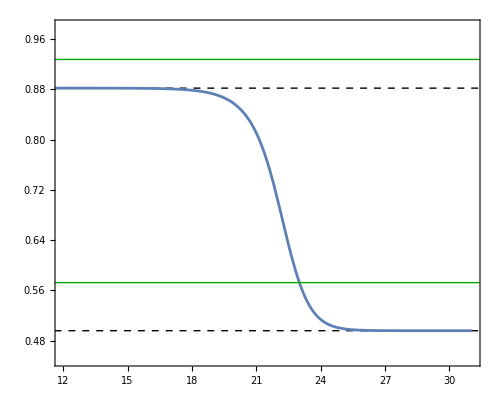

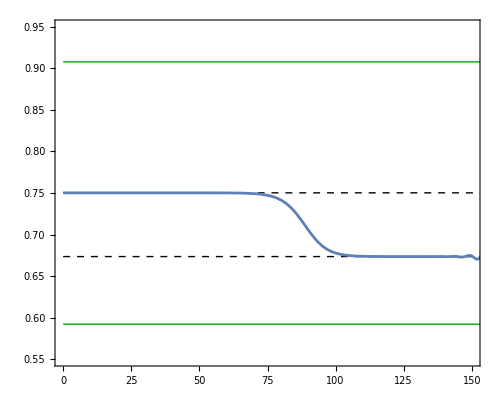

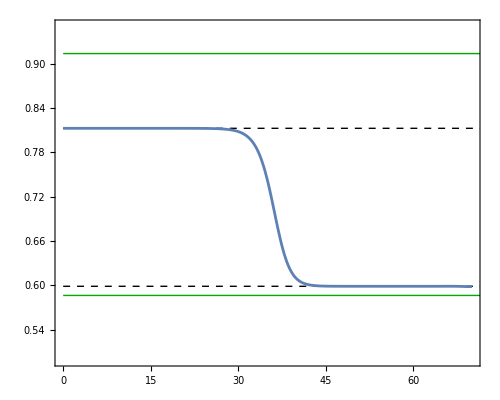

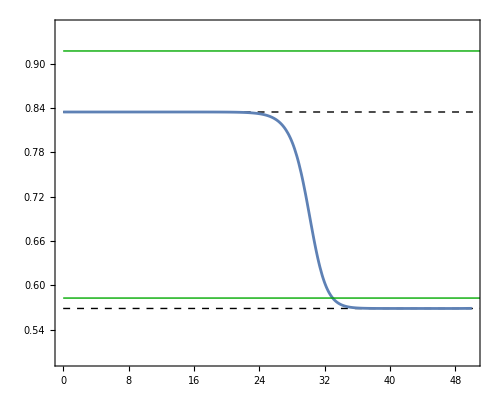

```mathematica
Needs["MaTeX`"]
(*Solutions for four representative examples*)
i=1;sol1=Quiet[solutionAndObjFn[1/2,data[[i]][[1]],data[[i]][[2]],data[[i]][[3]],data[[i]][[4]],data[[i]][[5]]]];
j=121;sol2=Quiet[solutionAndObjFn[1/2,data[[j]][[1]],data[[j]][[2]],data[[j]][[3]],data[[j]][[4]],data[[j]][[5]]]];
k=91;sol3=Quiet[solutionAndObjFn[1/2,data[[k]][[1]],data[[k]][[2]],data[[k]][[3]],data[[k]][[4]],data[[k]][[5]]]];
l=71;sol4=Quiet[solutionAndObjFn[1/2,data[[l]][[1]],data[[l]][[2]],data[[l]][[3]],data[[l]][[4]],data[[l]][[5]]]];

(*Example 1*)
Pe1=data[[i]][[1]];
SL1=(1/4)*(3+Sqrt[Pe1*Pe1-(1+β)^4/β^2]/Pe1)/.{β->1/2}; (*Spinodals*)
SG1=(1/4)*(3-Sqrt[Pe1*Pe1-(1+β)^4/β^2]/Pe1)/.{β->1/2};
LL1=Line[{{0,SL1},{200,SL1}}];(*Spinodal graphical objects*)
LG1=Line[{{0,SG1},{200,SG1}}];
PL1=data[[i]][[2]]; (*Weak coexistence densities*)
PG1=data[[i]][[3]];
LLL1=Line[{{0,PL1},{200,PL1}}]; (*Binodal graphical objects*)
LLG1=Line[{{0,PG1},{200,PG1}}];
Plot[{sol1[[1]]},{x,0,sol1[[2]]},PlotRange->{{12,sol1[[2]]},{0.45,0.98}},Prolog->{Directive[Black,Dashed],LLG1,LLL1},Epilog->{Directive[Darker[Green]],LG1,LL1},Frame->{ True,True,True,True},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,Axes->False,AspectRatio->4/5,FrameLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\phi^{\\rm st}(x)"}]

(*Example 2*)
Pe2=data[[j]][[1]];
SL2=(1/4)*(3+Sqrt[Pe2*Pe2-(1+β)^4/β^2]/Pe2)/.{β->1/2};(*Spinodals*)
SG2=(1/4)*(3-Sqrt[Pe2*Pe2-(1+β)^4/β^2]/Pe2)/.{β->1/2};
LL2=Line[{{0,SL2},{200,SL2}}];(*Spinodal graphical objects*)
LG2=Line[{{0,SG2},{200,SG2}}];
PL2=data[[j]][[2]];(*Weak coexistence densities*)
PG2=data[[j]][[3]];
LLL2=Line[{{0,PL2},{200,PL2}}];(*Binodal graphical objects*)
LLG2=Line[{{0,PG2},{200,PG2}}];
Plot[{sol2[[1]]},{x,0,205},PlotRange->{{0,150},{0.55,0.95}},Prolog->{Directive[Black,Dashed],LLG2,LLL2},Epilog->{Directive[Darker[Green]],LG2,LL2},Frame->{ True,True,True,True},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,Axes->False,AspectRatio->4/5,FrameLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\phi^{\\rm st}(x)"}]

(*Example 3*)
Pe3=data[[k]][[1]];
SL3=(1/4)*(3+Sqrt[Pe3*Pe3-(1+β)^4/β^2]/Pe3)/.{β->1/2};(*Spinodals*)
SG3=(1/4)*(3-Sqrt[Pe3*Pe3-(1+β)^4/β^2]/Pe3)/.{β->1/2};
LL3=Line[{{0,SL3},{210,SL3}}];(*Spinodal graphical objects*)
LG3=Line[{{0,SG3},{210,SG3}}];
PL3=data[[k]][[2]];(*Weak coexistence densities*)
PG3=data[[k]][[3]];
LLL3=Line[{{0,PL3},{200,PL3}}];(*Binodal graphical objects*)
LLG3=Line[{{0,PG3},{200,PG3}}];
Plot[{sol3[[1]]},{x,0,70},PlotRange->{{0,70},{0.5,0.95}},Prolog->{Directive[Black,Dashed],LLG3,LLL3},Epilog->{Directive[Darker[Green]],LG3,LL3},Frame->{ True,True,True,True},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,Axes->False,AspectRatio->4/5,FrameLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\phi^{\\rm st}(x)"}]

(*Example 4*)
Pe4=data[[l]][[1]];
SL4=(1/4)*(3+Sqrt[Pe4*Pe4-(1+β)^4/β^2]/Pe4)/.{β->1/2};(*Spinodals*)
SG4=(1/4)*(3-Sqrt[Pe4*Pe4-(1+β)^4/β^2]/Pe4)/.{β->1/2};
LL4=Line[{{0,SL4},{210,SL4}}];(*Spinodal graphical objects*)
LG4=Line[{{0,SG4},{210,SG4}}];
PL4=data[[l]][[2]];(*Weak coexistence densities*)
PG4=data[[l]][[3]];
LLL4=Line[{{0,PL4},{200,PL4}}];(*Binodal graphical objects*)
LLG4=Line[{{0,PG4},{200,PG4}}];
Plot[{sol4[[1]]},{x,0,50},PlotRange->{{0,50},{0.5,0.95}},Prolog->{Directive[Black,Dashed],LLG4,LLL4},Epilog->{Directive[Darker[Green]],LL4,LG4},Frame->{ True,True,True,True},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,Axes->False,AspectRatio->4/5,FrameLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\phi^{\\rm st}(x)"}]
```

```mathematica
Additional plot
```

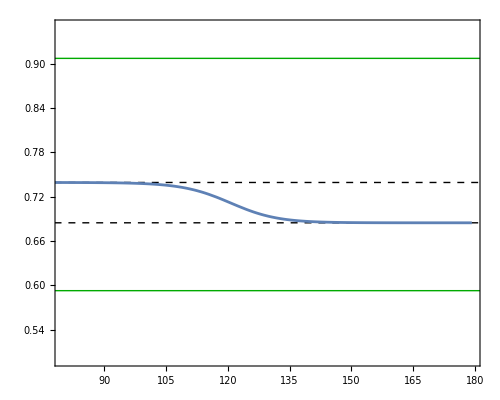

```mathematica
Needs["MaTeX`"]
l=124;sol4=Quiet[solutionAndObjFn[1/2,data[[l]][[1]],data[[l]][[2]],data[[l]][[3]],data[[l]][[4]],data[[l]][[5]]]];
Pe4=data[[l]][[1]];
SL4=(1/4)*(3+Sqrt[Pe4*Pe4-(1+β)^4/β^2]/Pe4)/.{β->1/2};(*Spinodals*)
SG4=(1/4)*(3-Sqrt[Pe4*Pe4-(1+β)^4/β^2]/Pe4)/.{β->1/2};
LL4=Line[{{0,SL4},{210,SL4}}];(*Spinodal graphical objects*)
LG4=Line[{{0,SG4},{210,SG4}}];
PL4=data[[l]][[2]];(*Weak coexistence densities*)
PG4=data[[l]][[3]];
LLL4=Line[{{0,PL4},{200,PL4}}];(*Binodal graphical objects*)
LLG4=Line[{{0,PG4},{200,PG4}}];
Plot[{sol4[[1]]},{x,0,sol4[[2]]},PlotRange->{{80,sol4[[2]]},{0.5,0.95}},Prolog->{Directive[Black,Dashed],LLG4,LLL4},Epilog->{Directive[Darker[Green]],LL4,LG4},Frame->{ True,True,True,True},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,Axes->False,AspectRatio->4/5,FrameLabel->(MaTeX[#,Magnification->24/12]&)/@{"x","\\phi^{\\rm st}(x)"}]
```